## Introduction

Questions:

1. Are there any fixed points?

## Main

### Simulation

<k> = -5.05

$Aborted

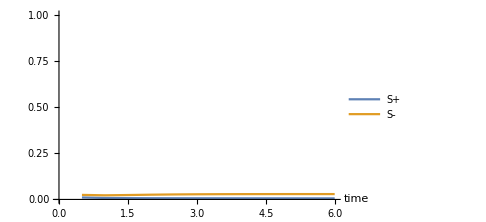
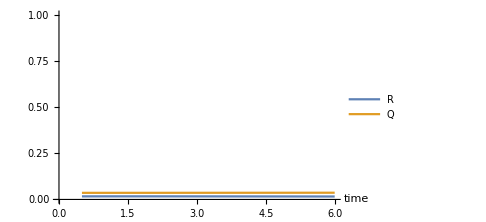
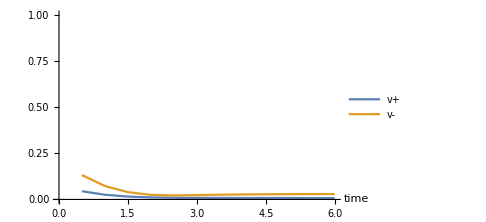
-Graphics- | -Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,2000,200};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.45,1,-10};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
results={};Dynamic[results]
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
results=plotResults[znew,js,ks]
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

#### No video

<k> = -5.05

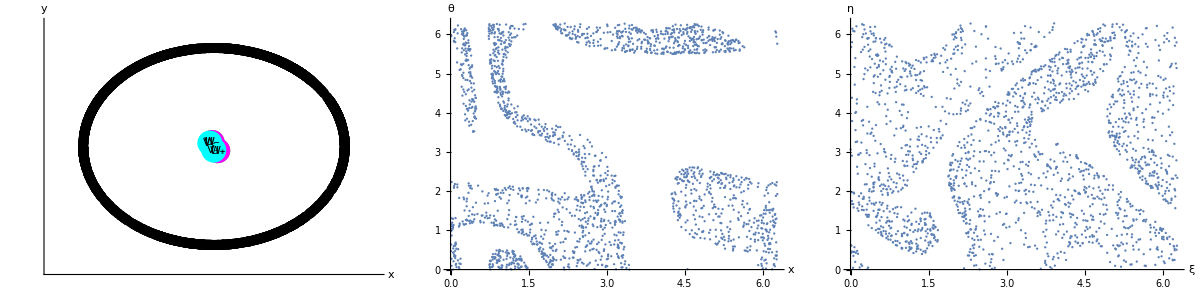

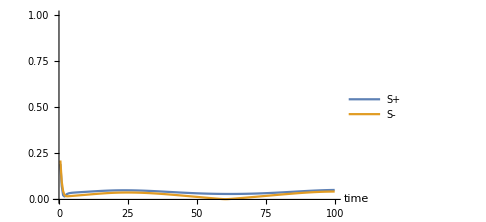
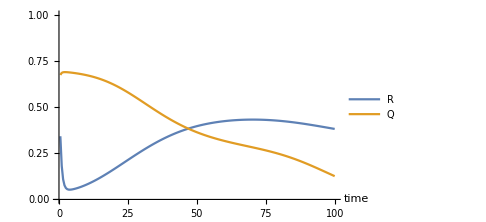
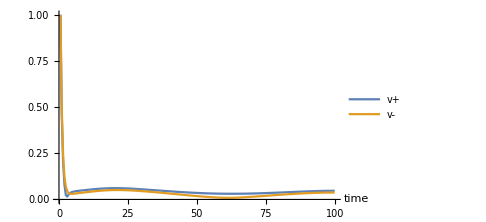
-Graphics- | -Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,2000,100};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.45,1,-10};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
results={};Dynamic[results];
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

### Start sync’d

<k> = -1.1

$Aborted

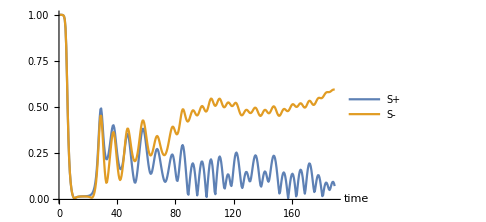
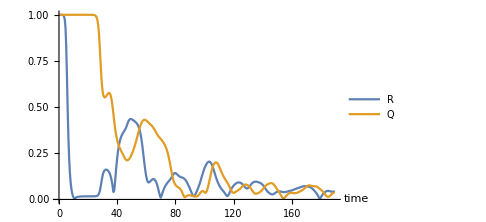
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,500};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.3,1,-2};
J=Table[1,{i,1,n}];
k =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,0.01}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
results={};Dynamic[results]
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
results=plotResults[znew]
];

p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

#### Note

Study decay from coherence

## Noisy phase wave

<k> = -1.25

<k> = -1.25

<k> = -1.25

«1 more identical outputs»

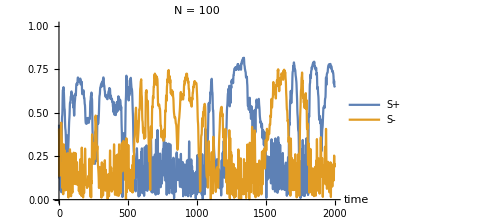
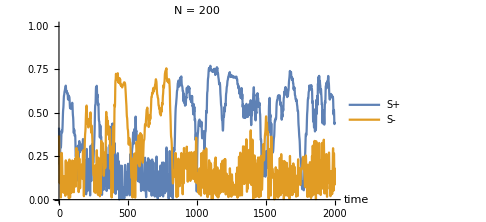
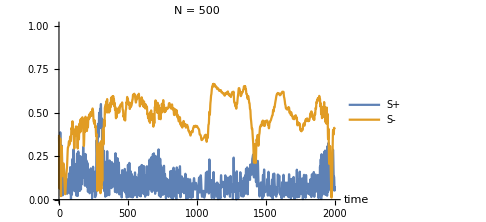
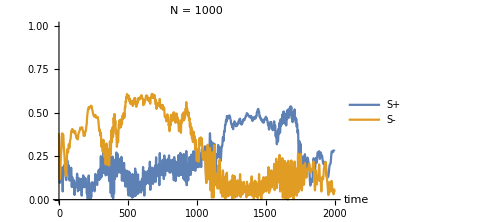

```mathematica
ParallelTable[
{dt,T}={0.5,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-3.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]];
{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1},PlotLabel->"N = "<>ToString[n]];
p1,
{n,{100,200,500,1000}}
]
```

<k> = -1.25

<k> = -1.25

<k> = -1.25

«1 more identical outputs»

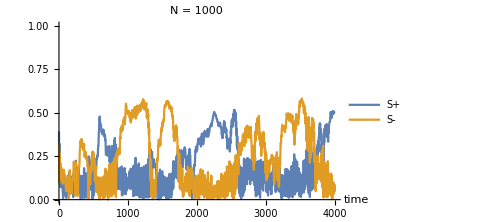

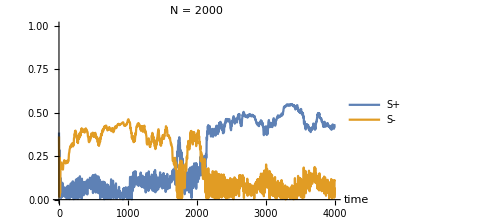

$Aborted

```mathematica
ParallelTable[
{dt,T}={0.5,4000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-3.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]];
{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1},PlotLabel->"N = "<>ToString[n]];
Print[p1];
p1,
{n,{1000,2000,5000,10000}}
]
```

## Catalog states

### Buckled phase wave

#### Main

<k> = -0.25

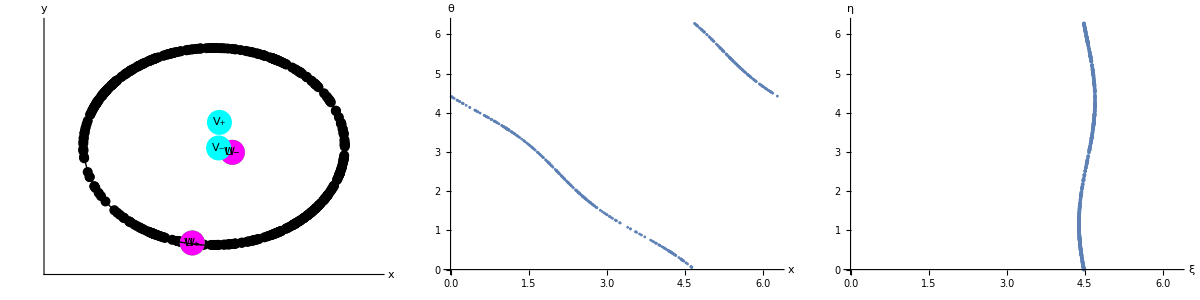

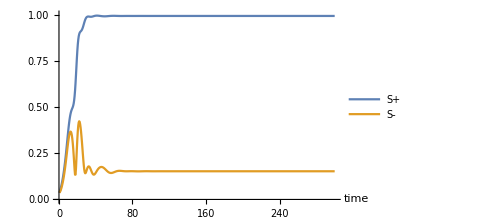
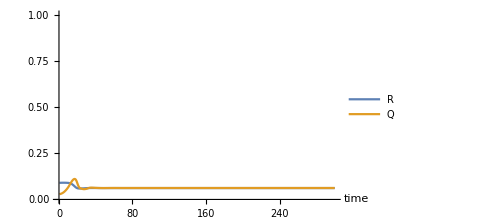
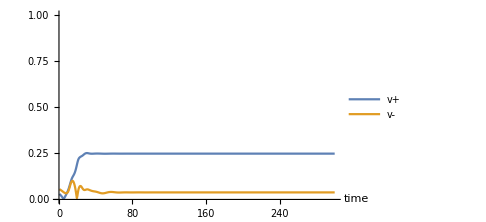
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[1];
{dt,n,T}={0.5,500,300};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

#### Search some space

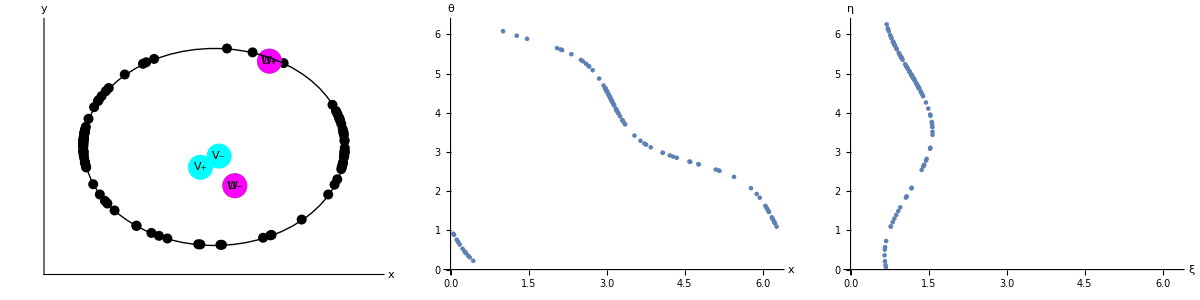
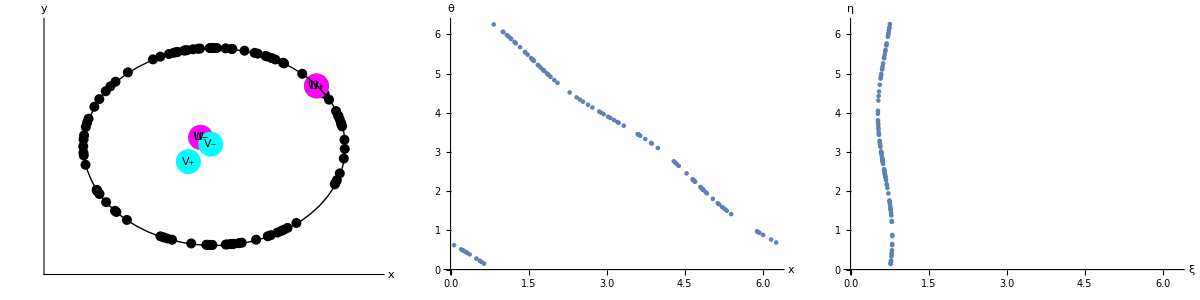
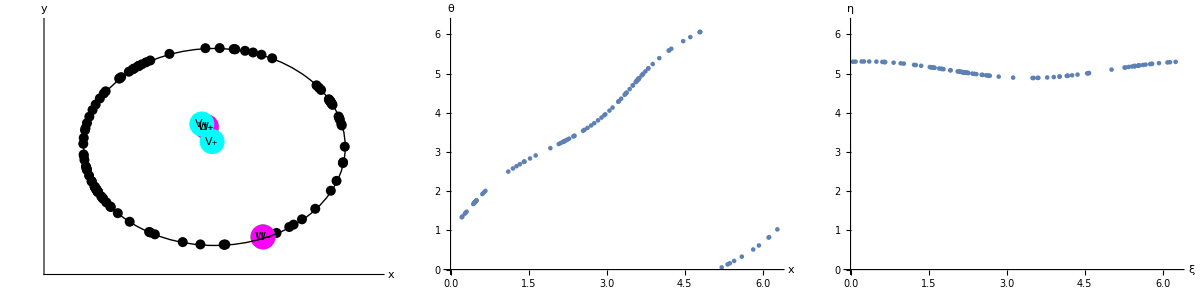
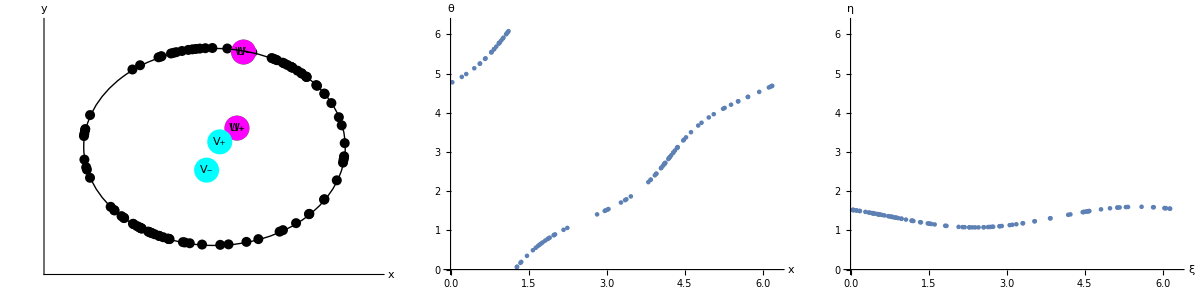
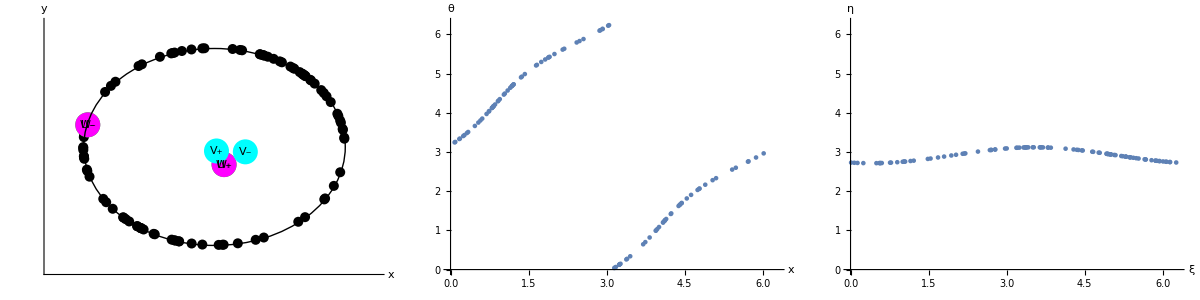
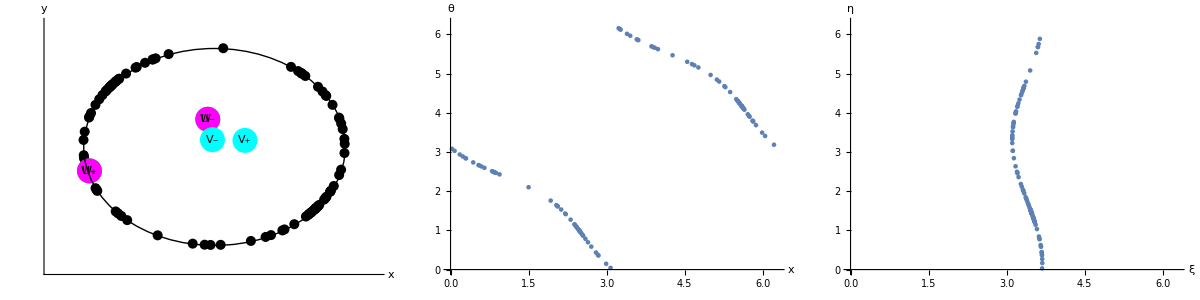
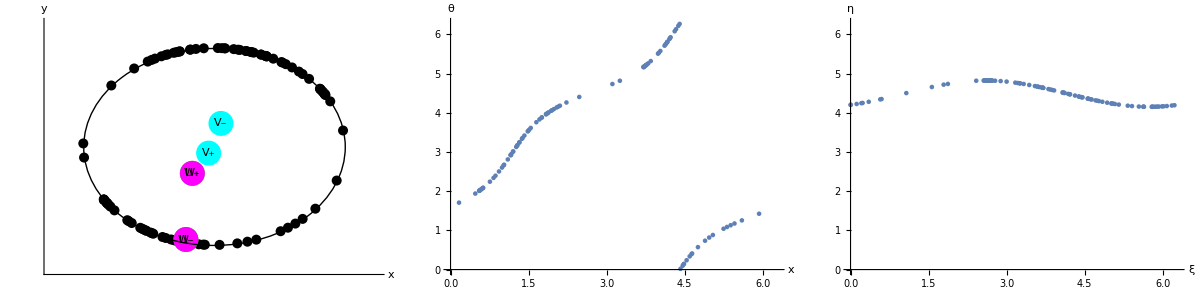
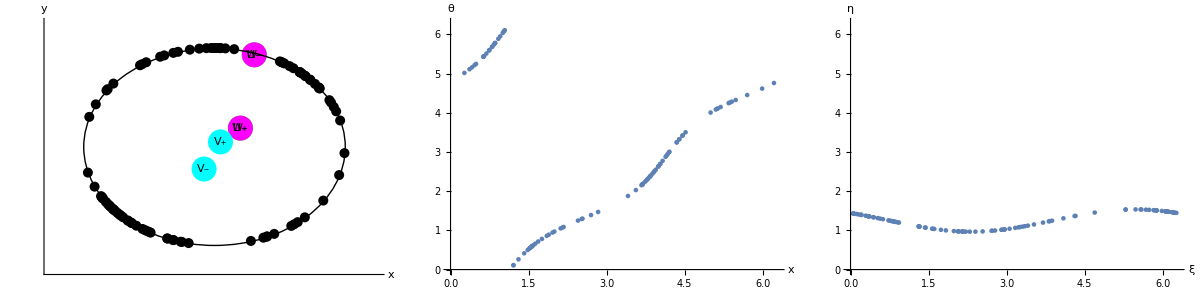

```mathematica
ParallelTable[
{dt,n,T}={0.5,100,300};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
];
plotResults[znew,js,ks],
{p,0.3,0.7,0.05}
]
```

#### Iterate over n

```mathematica
findBuckleWidth[znew_]:=Block[{x,θ,ξ,η,L,Wp,Wm},
{x,θ}=znew;
{ξ,η}={x+θ,x-θ}//mod;
{Wp,Wm}=findWs[znew];
If[Abs[Wp]<Abs[Wm],{ξ,η}={η,ξ}];
L=Max[ξ]-Min[ξ];
Return[L]
];
```

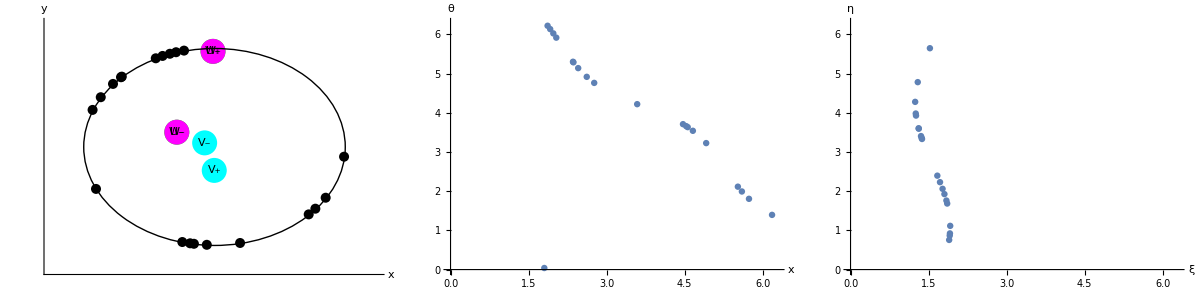

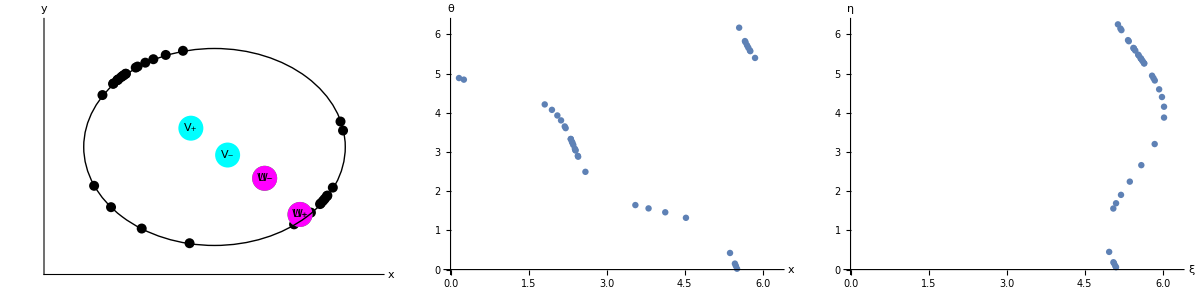

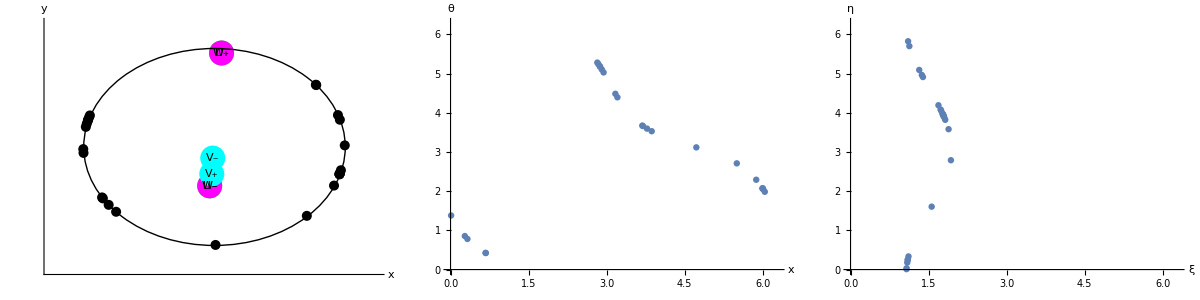

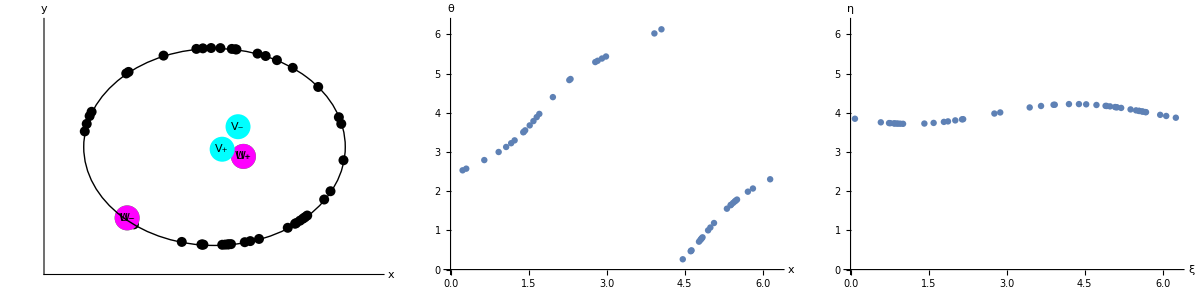

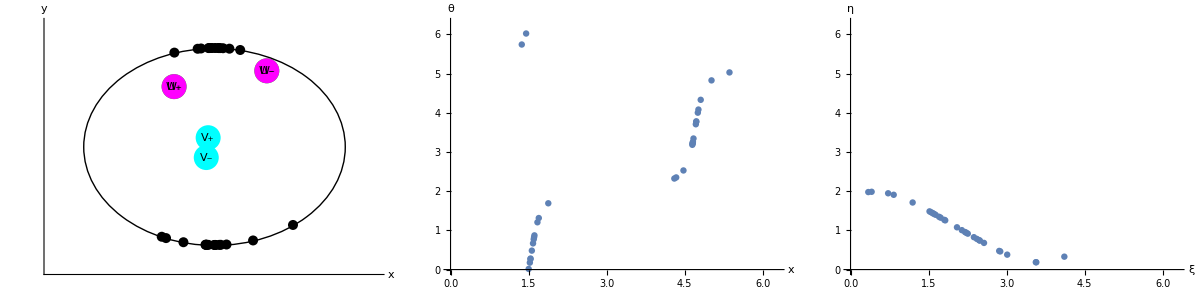

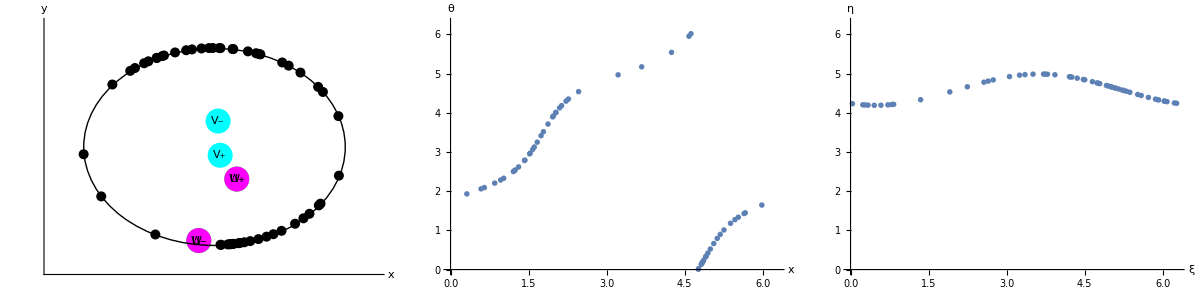

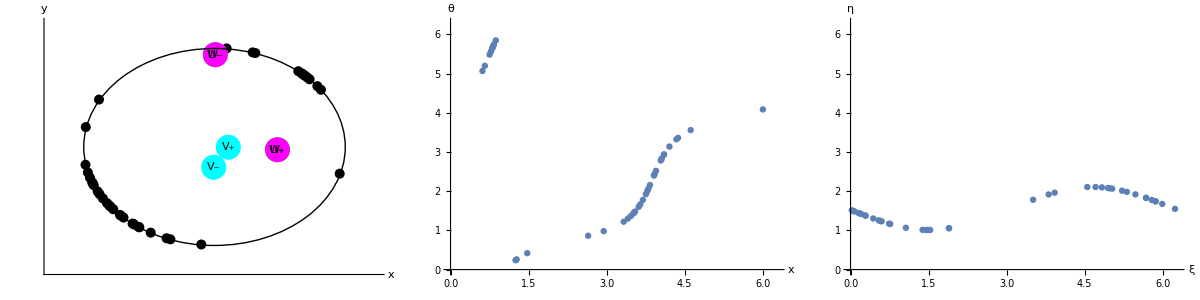

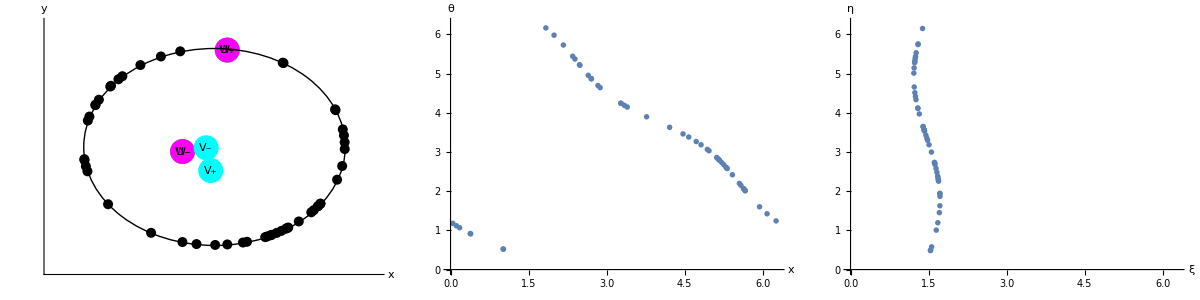

```mathematica
data=ParallelTable[
SeedRandom[0];
{dt,T}={0.25,1000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{ups,ums,Vp,Vm}=findVs[znew,js,ks];
If[Abs[ups]<Abs[ums],{ups,ums}={ums,ups}]
];
Print[plotResults[znew,js,ks]];
{n,Abs[ums]/Abs[ups],findBuckleWidth[znew]},
{n,20,100,5}
];

p1=ListPlot[data[[All,{2,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]}];
p2=Plot[2 ArcSin[u],{u,0,2}];
Show[p1,p2]
```

```mathematica
p1=ListPlot[data[[All,{2,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]}];
p2=Plot[2 ArcSin[u],{u,0,2}];
Show[p1,p2]
```

-Graphics-

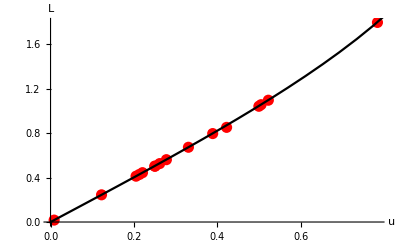

```mathematica
p1=ListPlot[data[[1;;-1,{2,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]},TicksStyle->Directive["Label", 12],PlotStyle->{PointSize[0.02],Red}];
p2=Plot[2 ArcSin[u],{u,0,2},PlotStyle->Black];
p3=Show[p1,p2]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["buckle-phase-wave-L-u.png",p3];
```

#### Larger n

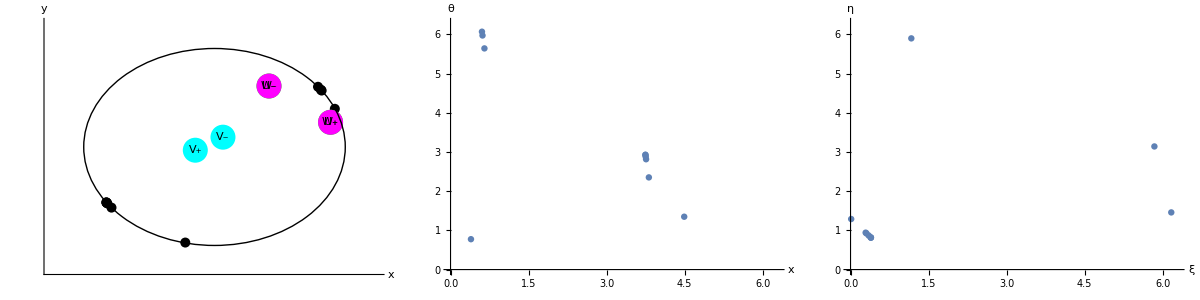

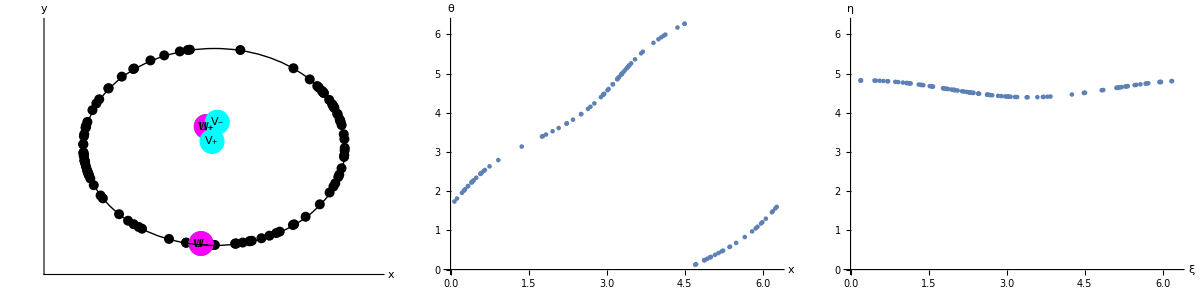

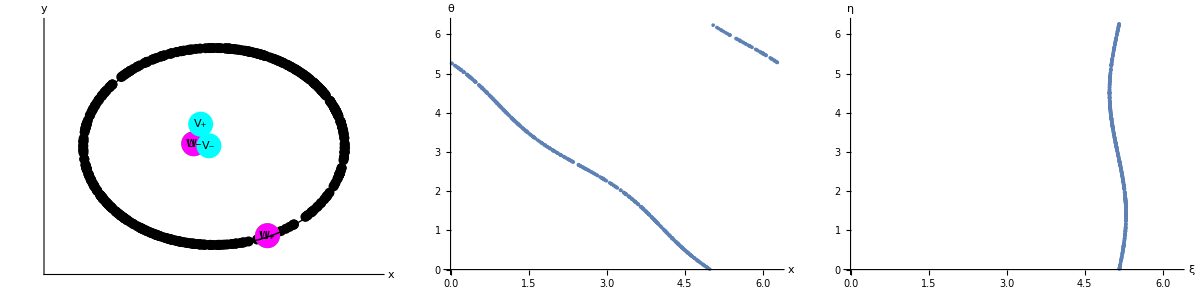

$Aborted

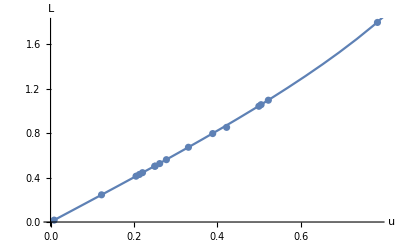

```mathematica
data=ParallelTable[
SeedRandom[0];
{dt,T}={0.25,200};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.5,1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{ups,ums,Vp,Vm}=findVs[znew,js,ks];
If[Abs[ups]<Abs[ums],{ups,ums}={ums,ups}]
];
Print[plotResults[znew,js,ks]];
{n,Abs[ums]/Abs[ups],findBuckleWidth[znew]},
{n,{10,100,500,1000}}
];

p1=ListPlot[data[[All,{2,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]}];
p2=Plot[2 ArcSin[u],{u,0,2}];
Show[p1,p2]
```

```mathematica
ListPlot[data[[All,{1,3}]],AxesLabel->{Style["u",17,Italic],Style["L",17,Italic]}]
```

```mathematica
2+2
```

4

### Breathing phase wave

<k> = -0.95

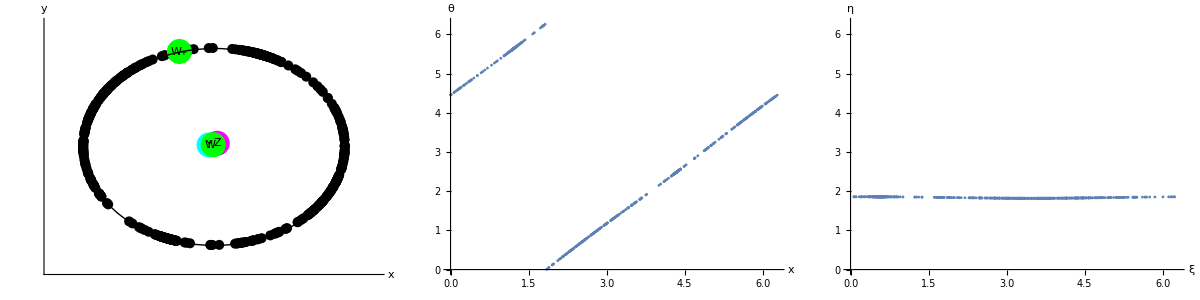

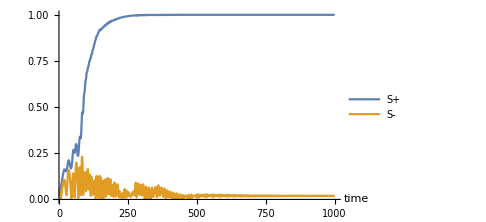
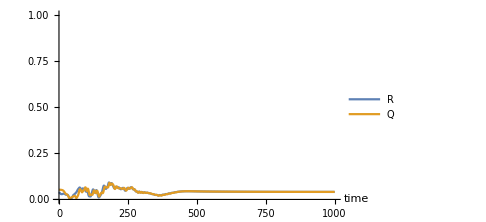
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,1000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.35,1,-2};
J=Table[1,{i,1,n}];
k =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Splay state

1. check stability 
2. breathing transient. 
3. Check time scale of relaxation -- glassy?

<k> = -0.95

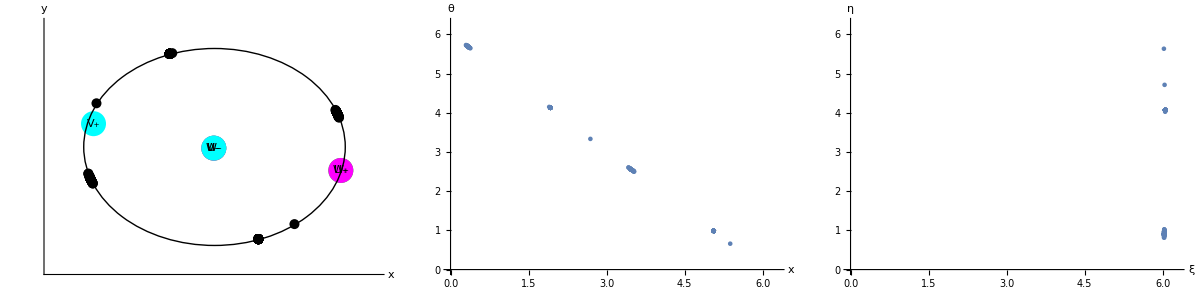

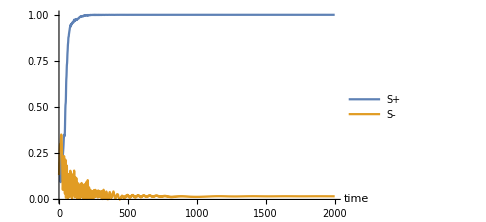
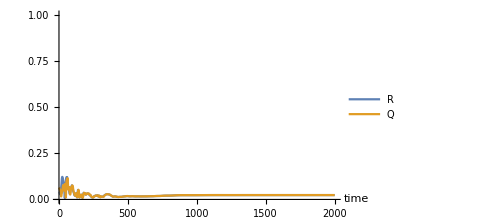
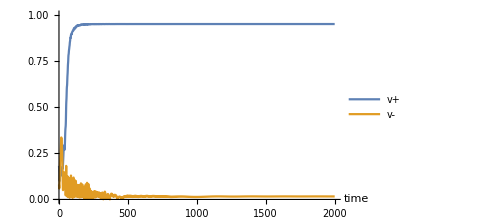
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,n,T}={0.5,200,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.35,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

<k> = -0.95

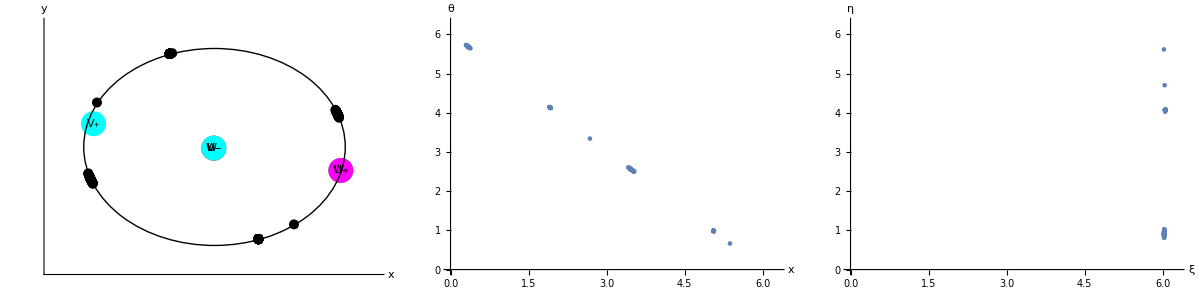

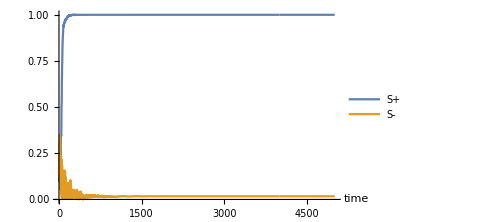
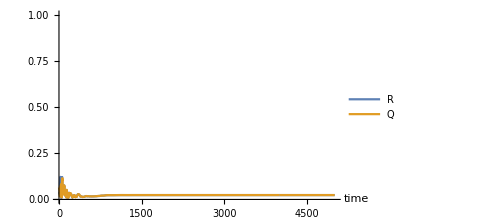
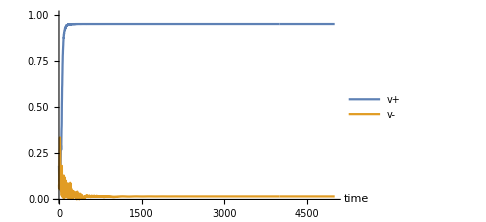
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,n,T}={0.5,200,5000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.35,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

<k> = -1.1

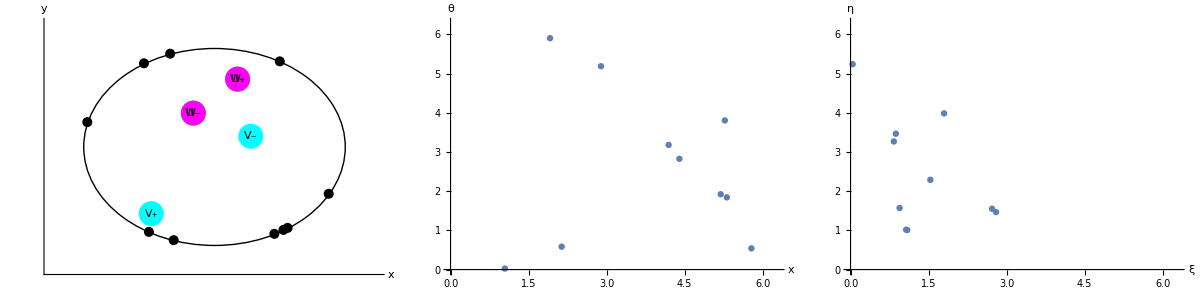

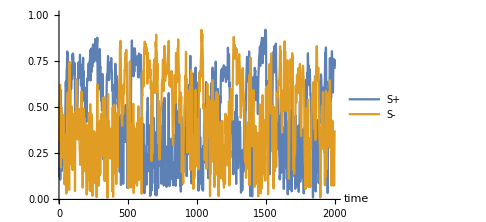
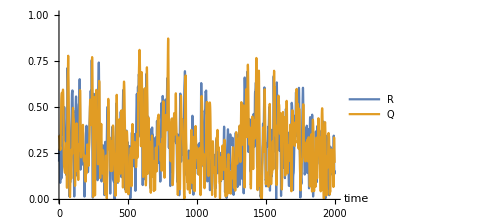
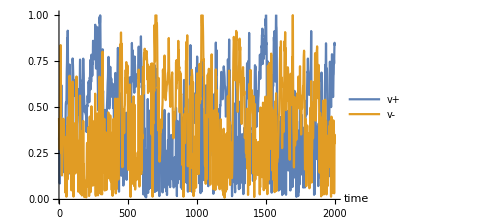
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,n,T}={0.5,10,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.35,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

<k> = -0.95

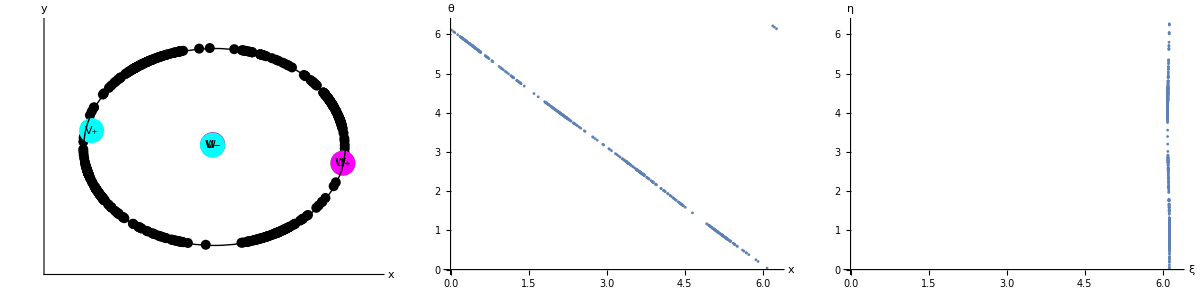

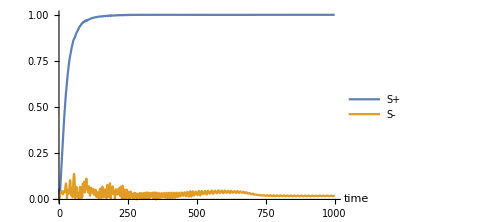
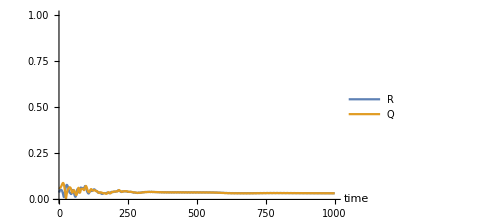
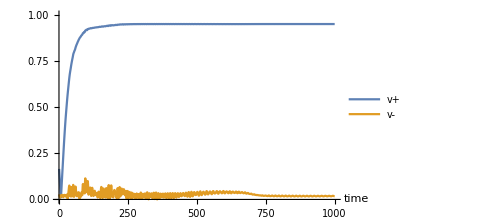
-Graphics- | -Graphics- | -Graphics-

```mathematica
SeedRandom[0];
{dt,n,T}={0.5,500,1000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.35,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[ks]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,Vps,Vms,ts}={{},{},{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];{Upos,Um,Vp,Vm}=findVs[znew,js,ks];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];AppendTo[Vps,Vp];AppendTo[Vms,Vm];
];
plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p3=ListPlot[{{ts,Vps//Abs}ᵀ,{ts,Vms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"v+","v-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2,p3}}]
```

### Dirty phase wave (IC different here)

<k> = -1.1

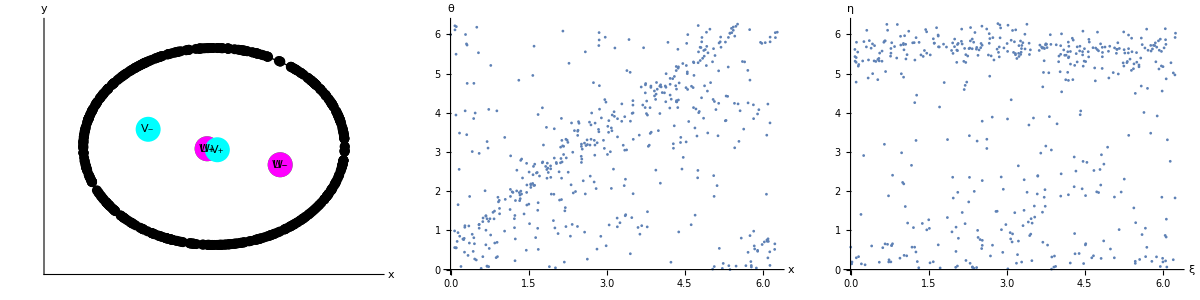

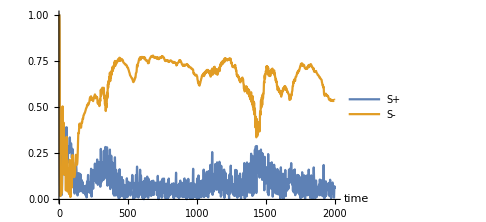
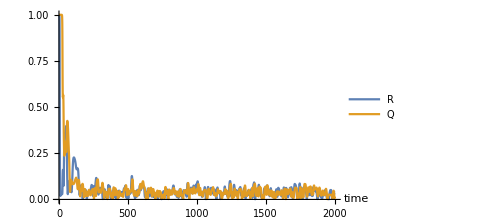
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.3,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,0.01}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
results=plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

<k> = -1.1

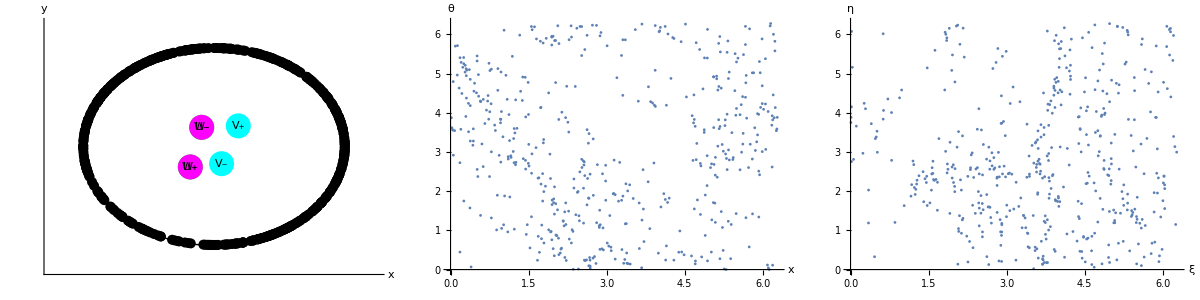

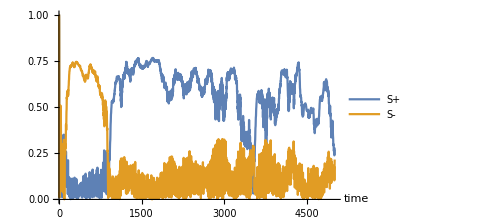
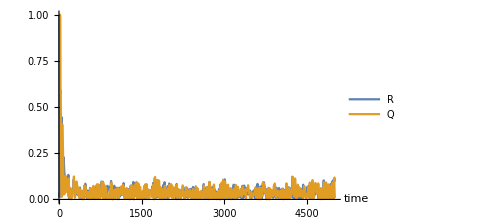
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,5000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.3,1,-2};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,0.01}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
results=plotResults[znew,js,ks]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Strands

<k> = -1.6

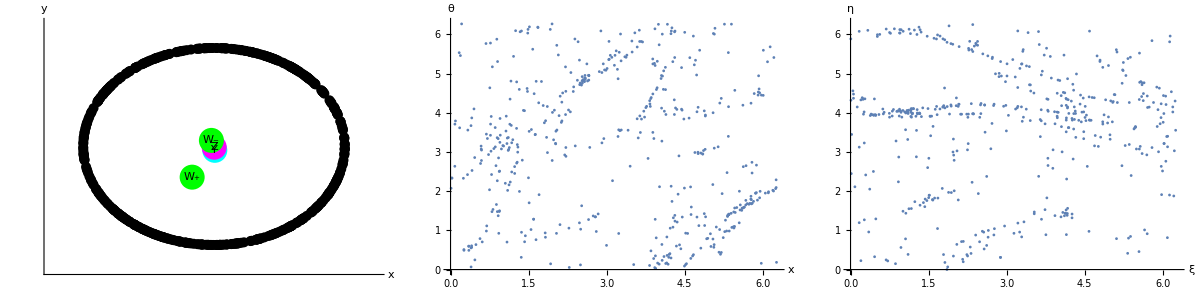

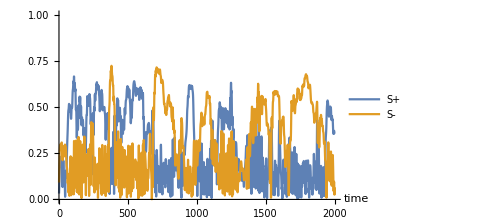
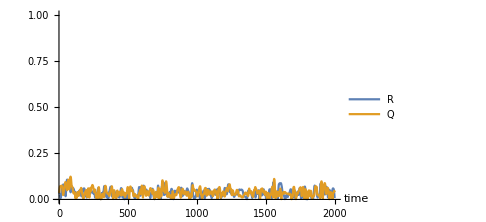
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.45,5,-7};
J=Table[1,{i,1,n}];
k =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

### Incoherence

<k> = -4.4

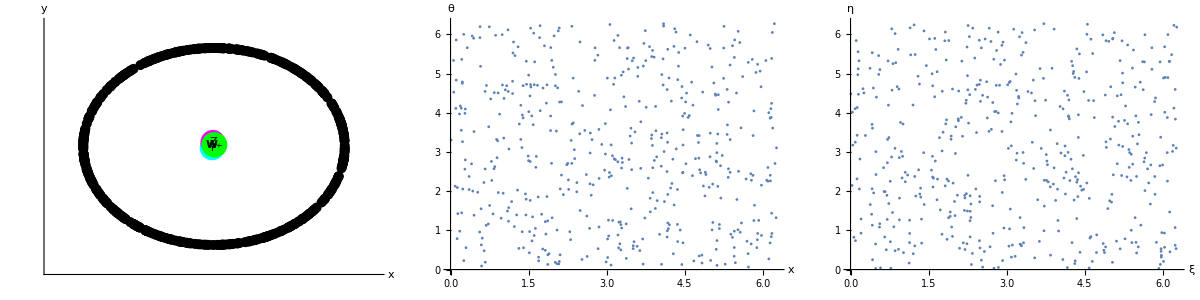

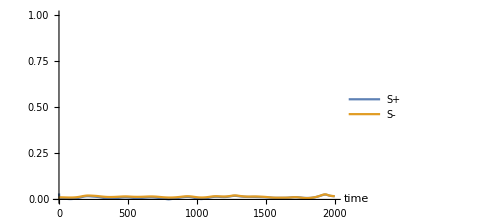
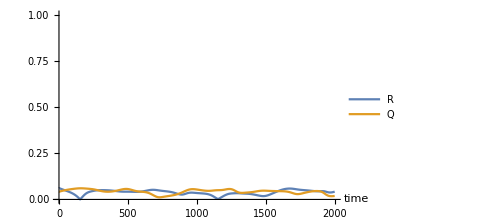
-Graphics- | -Graphics-

```mathematica
{dt,n,T}={0.5,500,2000};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2}={0.1,1,-5};
J=Table[1,{i,1,n}];
k =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
Print["<k> = "<>ToString[Mean[k]//N]]
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{Wps,Wms,Zs,Ys,ts}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,J,k];
z0=znew;t++;
{Wp,Wm}=findWs[znew];{Y,Z}=findRs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];AppendTo[Zs,Z];AppendTo[Ys,Y];AppendTo[ts,t*dt];
];
plotResults[znew]
p1=ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"S+","S-"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
p2=ListPlot[{{ts,Zs//Abs}ᵀ,{ts,Ys//Abs}ᵀ},AxesOrigin->{0,0},AxesLabel->{"time"},PlotLegends->{"R","Q"},Joined->True,ImageSize->Medium,PlotRange->{0,1}];
Grid[{{p1,p2}}]
```

## S(p)

### Methods

```mathematica
cleanOrderPar[orderpar_,cutoff_]:=Block[{index,meanOrderPar},
(*Takes the average of  x[cutoff;;-1]*)
index=Round[cutoff*Length[orderpar]];
meanOrderPar=Mean[orderpar[[index;;-1]]];
Return[meanOrderPar]
]
```

### Do sim:

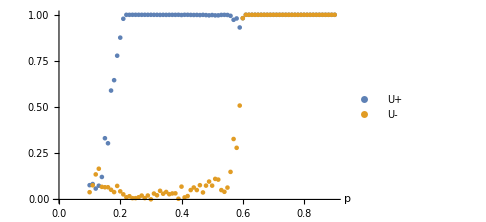
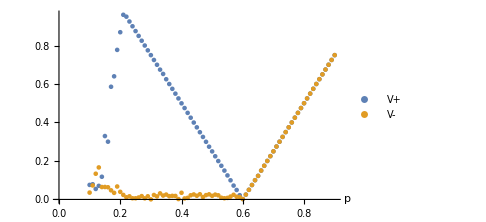
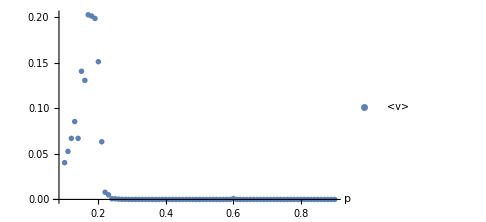
-Graphics- | -Graphics- | -Graphics-

```mathematica
data=ParallelTable[
cutoff=0.5;
{dt,n,T}={0.5,1000,500};  (*dt = timestep, n = number of swarmalators*)
{k1,k2}={1,-1.5};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{ups,ums,vps,vms,vs}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
vmean=findMeanV[znew,z0,dt];
z0=znew;t++;
{up,um,vp,vm}=Abs[findVs[znew,js,ks]];(*Notation clash here*)
AppendTo[ups,up];AppendTo[ums,um];AppendTo[vps,vp];AppendTo[vms,vm];AppendTo[vs,vmean];
];
If[ups[[-1]]<ums[[-1]],{ups,ums}={ums,ups}];
If[vps[[-1]]<vms[[-1]],{vps,vms}={vms,vps}];
{ups,ums,vps,vms,vs}={cleanOrderPar[ups,cutoff],cleanOrderPar[ums,cutoff],cleanOrderPar[vps,cutoff],cleanOrderPar[vms,cutoff],cleanOrderPar[vs,cutoff]};
{p,ups,ums,vps,vms,vs},
{p,0.1,0.9,0.01}
];

p1=ListPlot[Table[data[[All,{1,i}]],{i,2,3}],AxesLabel->{"p"},PlotLegends->{"U+","U-"},ImageSize->Medium];
p2=ListPlot[Table[data[[All,{1,i}]],{i,4,5}],AxesLabel->{"p"},PlotLegends->{"V+","V-"},ImageSize->Medium];
p3=ListPlot[Table[data[[All,{1,i}]],{i,6,6}],AxesLabel->{"p"},PlotLegends->{"<v>"},ImageSize->Medium,PlotRange->All];
Grid[{{p1,p2,p3}}]
```

```mathematica
Mean[{1,-1.5}]
```

-0.25

```mathematica
Plot[]
```

### Along strand line: {p,k1,k2}={0.45,5,-7};

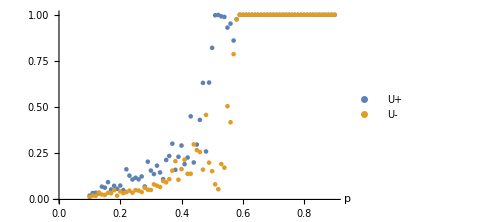
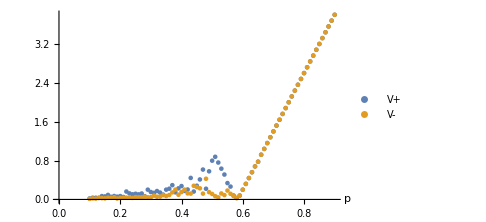
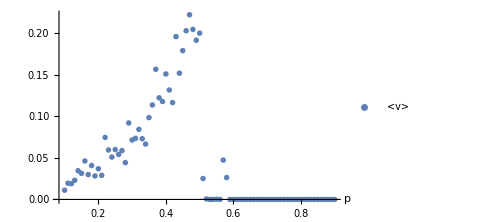
-Graphics- | -Graphics- | -Graphics-

```mathematica
data=ParallelTable[
cutoff=0.5;
{dt,n,T}={0.5,500,500};  (*dt = timestep, n = number of swarmalators*)
{k1,k2}={5,-7};
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
{ups,ums,vps,vms,vs}={{},{},{},{},{}};
{t,NT}={0,Floor[T/dt]} ; 
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
vmean=findMeanV[znew,z0,dt];
z0=znew;t++;
{up,um,vp,vm}=Abs[findVs[znew,js,ks]];(*Notation clash here*)
AppendTo[ups,up];AppendTo[ums,um];AppendTo[vps,vp];AppendTo[vms,vm];AppendTo[vs,vmean];
];
If[ups[[-1]]<ums[[-1]],{ups,ums}={ums,ups}];
If[vps[[-1]]<vms[[-1]],{vps,vms}={vms,vps}];
{ups,ums,vps,vms,vs}={cleanOrderPar[ups,cutoff],cleanOrderPar[ums,cutoff],cleanOrderPar[vps,cutoff],cleanOrderPar[vms,cutoff],cleanOrderPar[vs,cutoff]};
{p,ups,ums,vps,vms,vs},
{p,0.1,0.9,0.01}
];

p1=ListPlot[Table[data[[All,{1,i}]],{i,2,3}],AxesLabel->{"p"},PlotLegends->{"U+","U-"},ImageSize->Medium];
p2=ListPlot[Table[data[[All,{1,i}]],{i,4,5}],AxesLabel->{"p"},PlotLegends->{"V+","V-"},ImageSize->Medium];
p3=ListPlot[Table[data[[All,{1,i}]],{i,6,6}],AxesLabel->{"p"},PlotLegends->{"<v>"},ImageSize->Medium,PlotRange->All];
Grid[{{p1,p2,p3}}]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real,1},{k,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J[[j]]*Sin[xji] Cos[thetaji];
thetatemp=k[[j]]*Sin[thetaji] Cos[xji];
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
];

findVs[z_,j_,k_]:=Block[{Upos,Um,Vp,Vm,i,numOsc},
{Upos,Um,Vp,Vm}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Upos+=j[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Um+=j[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Vp+=k[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Vm+=k[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Upos/numOsc,Um/numOsc,Vp/numOsc,Vm/numOsc}]
];

findRs[z_]:=Block[{Z,Y,i,numOsc},
{Z,Y}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Y+=Exp[ⅈ (z[[1,i]])];
Z+=Exp[ⅈ (z[[2,i]])];
];
Return[{Y/numOsc,Z/numOsc}]
]

plotResults[z_,js_,ks_]:=Block[{colors,Wp,Wm,Vp,Vm,Rx,Rtheta,p1,p2,p3,Upos,Um},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
{Upos,Um,Vp,Vm}=findVs[z,js,ks];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],
Magenta,Point[{Upos//Re,Upos//Im}],Black,Text["U_+",{Upos//Re,Upos//Im}],
Magenta,Point[{Um//Re,Um//Im}],Black,Text["U_-",{Um//Re,Um//Im}],
Cyan,Point[{Vp//Re,Vp//Im}],Black,Text["V_+",{Vp//Re,Vp//Im}],
Cyan,Point[{Vm//Re,Vm//Im}],Black,Text["V_-",{Vm//Re,Vm//Im}],

(*Domain*)
Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{Mod[z[[1,All]],2π],Mod[z[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{Mod[z[[1,All]]+z[[2,All]],2π],Mod[z[[1,All]]-z[[2,All]],2π]}ᵀ,PlotRange->{{0π,2π},{0π,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];


eulerStep1D[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k];
k2=F[z+dt/2 k1,n,J,k];
k3=F[z+dt/2 k2,n,J,k];
k4=F[z+dt k3,n,J,k];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
]
```